```mathematica
FinancialData["^GSPC", "Price"]
```

2884.05

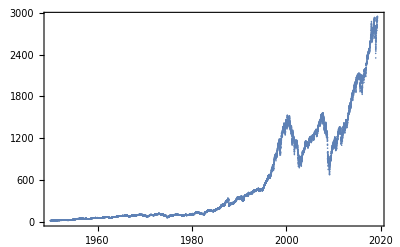

```mathematica
DateListPlot[
FinancialData["^GSPC", "Price", All], Joined->False]
```

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
DateListPlot[
list, Joined->False]]
```

-Graphics-

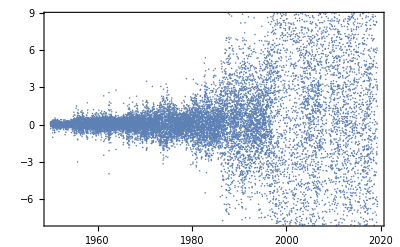

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]
```

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
Take[Reverse@SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Last],10]]
```

{{{2018,12,24},116.6},{{2008,10,10},104.13},{{2008,10,27},91.59},{{2019,1,3},84.05},{{2015,8,25},72.9},{{2018,3,23},70.29},{{2000,3,15},66.33},{{2001,1,2},64.29},{{2018,11,27},61.6201},{{2008,9,29},59.9399}}

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
Column@Take[
Reverse@
SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list],
Ratios@
Map[Last,list]
}], Last],10]]
```

{{2008,10,10},104.13,1.1158}
{{2008,10,27},91.59,1.10789}
{{1987,10,20},21.55,1.09099}
{{2009,3,20},54.38,1.07076}
{{2008,11,12},58.99,1.06921}
{{2008,11,21},51.78,1.06472}
{{2009,3,9},43.0699,1.06366}
{{2008,11,20},47.59,1.06325}
{{2002,7,23},45.73,1.05733}
{{2008,9,29},59.9399,1.05417}

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
Column@Take[
Reverse@
SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list],
Map[100(#-1)&,Ratios@
Map[Last,list]]
}], Last],10]]
```

{{2008,10,10},104.13,11.58}
{{2008,10,27},91.59,10.789}
{{1987,10,20},21.55,9.09936}
{{2009,3,20},54.38,7.07575}
{{2008,11,12},58.99,6.92127}
{{2008,11,21},51.78,6.47225}
{{2009,3,9},43.0699,6.3663}
{{2008,11,20},47.59,6.32476}
{{2002,7,23},45.73,5.73273}
{{2008,9,29},59.9399,5.41747}

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
Column@Take[
Reverse@
SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list],
Map[100(#-1)&,Ratios@
Map[Last,list]]
}], Last],20]]
```

{{2008,10,10},104.13,11.58}
{{2008,10,27},91.59,10.789}
{{1987,10,20},21.55,9.09936}
{{2009,3,20},54.38,7.07575}
{{2008,11,12},58.99,6.92127}
{{2008,11,21},51.78,6.47225}
{{2009,3,9},43.0699,6.3663}
{{2008,11,20},47.59,6.32476}
{{2002,7,23},45.73,5.73273}
{{2008,9,29},59.9399,5.41747}
{{2002,7,26},46.12,5.40781}
{{1987,10,19},11.99,5.33268}
{{2008,12,15},44.61,5.13603}
{{1997,10,27},44.86,5.11522}
{{1998,9,4},49.57,5.0899}
{{1970,5,26},3.48,5.02236}
{{2001,1,2},64.29,5.00986}
{{2018,12,24},116.6,4.95937}
{{1987,10,28},11.49,4.92541}
{{2008,10,17},44.85,4.76849}

```mathematica
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
Column@Take[
Reverse@
SortBy[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list],
Map[100(#-1)&,Ratios@
Map[Last,list]]
}], Last],20]]]
```

{{2008,10,10},104.13,11.58}
{{2008,10,27},91.59,10.789}
{{1987,10,20},21.55,9.09936}
{{2009,3,20},54.38,7.07575}
{{2008,11,12},58.99,6.92127}
{{2008,11,21},51.78,6.47225}
{{2009,3,9},43.0699,6.3663}
{{2008,11,20},47.59,6.32476}
{{2002,7,23},45.73,5.73273}
{{2008,9,29},59.9399,5.41747}
{{2002,7,26},46.12,5.40781}
{{1987,10,19},11.99,5.33268}
{{2008,12,15},44.61,5.13603}
{{1997,10,27},44.86,5.11522}
{{1998,9,4},49.57,5.0899}
{{1970,5,26},3.48,5.02236}
{{2001,1,2},64.29,5.00986}
{{2018,12,24},116.6,4.95937}
{{1987,10,28},11.49,4.92541}
{{2008,10,17},44.85,4.76849}

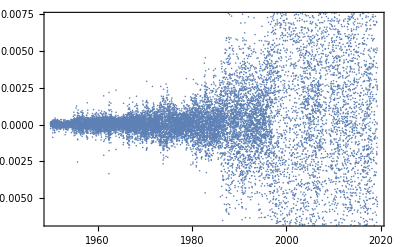

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Normalize@
Differences@
Map[Last,list]
}], Joined->False]]
```

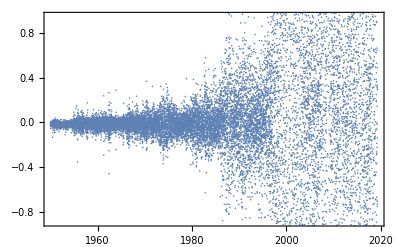

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Standardize@
Differences@
Map[Last,list]
}], Joined->False]]
```

```mathematica
With[{list=FinancialData["^GSPC", "Price", All]},
Standardize@
Differences@
Map[Last,list]]
```

{0.00284303,-0.00934846,-0.0126735,17442,-1.47785,-5.38465}
 |  |  |  |

```mathematica
Max[%13]
```

12.9047

```mathematica
Median[%13]
```

-0.0126735

```mathematica
GeometricMean[%13]
```

0.107697+0.0000193925 ⅈ

```mathematica
Mean[%13]
```

-2.40282×10^-17

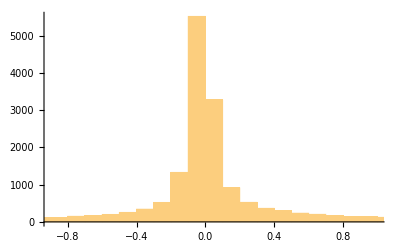

```mathematica
Histogram[%13]
```

```mathematica
Total@Out@13
```

-4.1922×10^-13

```mathematica
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

-Graphics-

```mathematica
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False, PlotRange->{]]]
```

```mathematica
Max@
Map[Last,
FinancialData["^GSPC", "Price", All]]
```

2945.83

```mathematica
Min@
Map[Last,
FinancialData["^GSPC", "Price", All]]
```

16.66

```mathematica
With[{list=Differences@
Map[Last,FinancialData["^GSPC", "Price", All]]},
Table[func->func[list],
{func, {Max,Min,Mean,Median}}]]
```

{Max→116.6,Min→-113.19,Mean→0.164349,Median→0.0499992}

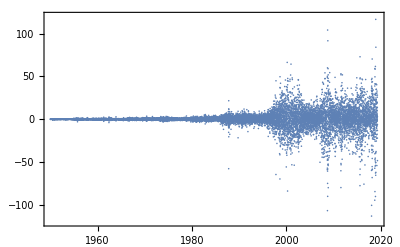

```mathematica
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False, PlotRange->{-120,120}]]]
```

```mathematica
Manipulate[
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False, PlotRange->{-a,a}]]],
{{a,120},1,130, 1}]
```

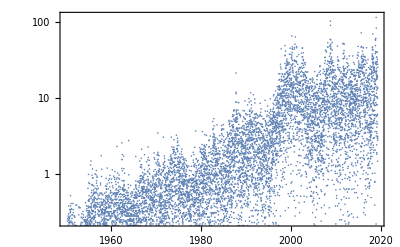

```mathematica
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
DateListLogPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False, PlotRange->{-120,120}]]]
```

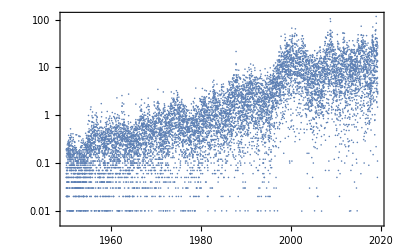

```mathematica
With[{index="^GSPC"},
With[{list=FinancialData[index, "Price", All]},
DateListLogPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

```mathematica
Log[x,1]
```

0

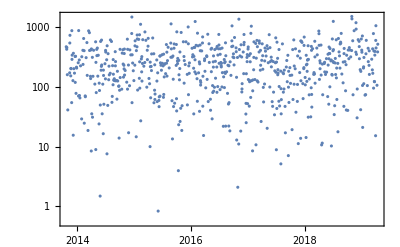

```mathematica
With[{index="^IPC"},
With[{list=FinancialData[index, "Price", All]},
DateListLogPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

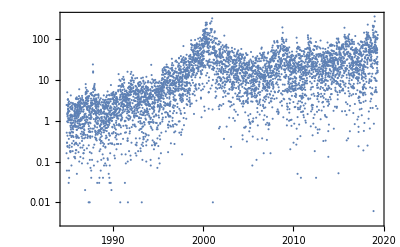

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
DateListLogPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

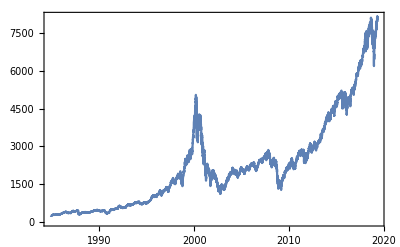

```mathematica
DateListPlot[
FinancialData["^IXIC", "Price", All], Joined->True]
```

```mathematica
CountryData[]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
CountryData[]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
cd[c_,p_]:=CountryData[c,p]
```

```mathematica
Reverse@
SortBy[
Map[#->cd[#, "GDP"]/cd[#,"Population"]&,
CountryData[]], Last]
```

Power::infy: Infinite expression 1/0 encountered.

{Bouvet Island→Missing[NotAvailable] (ComplexInfinity per person),Liechtenstein→165845. $,Monaco→156994. $,Luxembourg→100490. $,Bermuda→90852.5 $,Isle of Man→80586.8 $,Switzerland→78911.1 $,Macau→71964.4 $,Norway→69943.3 $,Ireland→64015.3 $,Iceland→59838.6 $,Qatar→57764.2 $,United States→57401.5 $,Denmark→53527. $,Jersey→53273.7 $,Faroe Islands→53022.1 $,Cayman Islands→52096.9 $,Singapore→52020.3 $,Sweden→51909.5 $,Australia→49267.4 $,San Marino→47626. $,Netherlands→45622.8 $,Austria→44737.2 $,Finland→43181.8 $,Germany→42353.2 $,Hong Kong→42082. $,Guernsey→41795.6 $,Canada→41769.1 $,Belgium→40943.4 $,United Kingdom→40009.6 $,Greenland→39312.7 $,New Zealand→39306.5 $,Turks and Caicos Islands→38953.3 $,Japan→38751.1 $,France→37942. $,Andorra→37140.5 $,United Arab Emirates→37099.8 $,Falkland Islands→37007. $,Brunei→36137.5 $,United States Virgin Islands→35891. $,Israel→35579.3 $,Guam→35273.9 $,Gibraltar→31992.1 $,Italy→31316. $,British Virgin Islands→29144.4 $,Bahamas→28484.9 $,Puerto Rico→28154.8 $,South Korea→27681.1 $,Kuwait→26804. $,Spain→26691.3 $,Malta→25529.6 $,Aruba→24552.2 $,Northern Mariana Islands→22522.8 $,Bahrain→21559.3 $,Slovenia→21494.8 $,Trinidad and Tobago→20309.1 $,Portugal→19830.2 $,Sint Maarten→19775.7 $,Saudi Arabia→19625.8 $,Czech Republic→18393.2 $,Taiwan→18073. $,Curacao→17883.5 $,Estonia→17820.2 $,Greece→17266.6 $,Cyprus→16995.5 $,Slovakia→16478.4 $,Saint Kitts and Nevis→16439.7 $,Martinique→15892.6 $,Barbados→15578.2 $,Uruguay→15164.5 $,Venezuela→15084.5 $,Seychelles→15066.2 $,Lithuania→14787. $,Antigua and Barbuda→14313.5 $,Oman→14298.9 $,Palau→14278.1 $,Cook Islands→14255.4 $,Anguilla→14164.2 $,Latvia→14142.2 $,Chile→13682.2 $,Panama→13465.1 $,Hungary→12942. $,Réunion→12434.9 $,Argentina→12379.5 $,Poland→12348.9 $,Croatia→12105.7 $,American Samoa→11825.8 $,Montserrat→10708.9 $,Turkey→10696.8 $,Costa Rica→10417.7 $,Grenada→9795.4 $,New Caledonia→9709.68 $,Maldives→9681.23 $,Mauritius→9618.27 $,Romania→9532.45 $,Malaysia→9376.85 $,Saint Lucia→9321.41 $,Russia→8911.49 $,Brazil→8582.36 $,Equatorial Guinea→8428.57 $,Lebanon→8154.54 $,Mexico→8105.42 $,China→7945.38 $,Dominica→7865.86 $,Guadeloupe→7814.17 $,Saint Pierre and Miquelon→7642.41 $,Cuba→7586.9 $,Kazakhstan→7540.9 $,Bulgaria→7514.62 $,Gabon→7018.57 $,Saint Vincent and the Grenadines→6990.4 $,Montenegro→6954.54 $,Botswana→6799.06 $,Dominican Republic→6648.42 $,Turkmenistan→6283.33 $,Niue→6186.65 $,Peru→5975.58 $,Ecuador→5931.72 $,Thailand→5895.72 $,Suriname→5818.98 $,Colombia→5756.83 $,Nauru→5588.46 $,French Guiana→5485.78 $,Macedonia→5232.24 $,South Africa→5209.29 $,Fiji→5194.5 $,Iran→5162.18 $,Wallis and Futuna Islands→5096.41 $,French Polynesia→5022.86 $,Belarus→5006.92 $,West Bank→4905.47 $,Jamaica→4863.48 $,Bosnia and Herzegovina→4821.84 $,Belize→4646.89 $,Libya→4573.25 $,Guyana→4502.61 $,Iraq→4480.49 $,Saint Helena, Ascension and Tristan da Cunha→4445.54 $,Serbia→4356.92 $,Namibia→4320.75 $,El Salvador→4201.64 $,Guatemala→4065.58 $,Albania→4048.84 $,Paraguay→4026.26 $,Samoa→4003.04 $,Jordan→3984.06 $,Sri Lanka→3895.3 $,Azerbaijan→3851.17 $,Algeria→3849.38 $,Tonga→3717.48 $,Georgia→3675.3 $,Marshall Islands→3661. $,Tunisia→3647.42 $,Mongolia→3636.13 $,Armenia→3607.74 $,Kosovo→3576.74 $,Indonesia→3531.4 $,Angola→3446.23 $,Egypt→3411.38 $,Cape Verde→3343.82 $,Bolivia→3058.96 $,Tuvalu→3057.44 $,Philippines→2906.13 $,Morocco→2898.92 $,Vanuatu→2800.07 $,Bhutan→2739.74 $,Eswatini→2721.26 $,Papua New Guinea→2449.74 $,Sudan→2358.17 $,Honduras→2322.37 $,Laos→2318.89 $,Syria→2211.57 $,Vietnam→2148.57 $,Nigeria→2119.86 $,Ukraine→2109.1 $,Uzbekistan→2106.52 $,Nicaragua→2041.4 $,Solomon Islands→1966.37 $,Mayotte→1844.73 $,Djibouti→1804.63 $,India→1690.43 $,São Tomé and Príncipe→1677.61 $,Moldova→1617.09 $,Kiribati→1559.75 $,Ivory Coast→1497.14 $,Republic of the Congo→1489.05 $,Ghana→1480.56 $,Kenya→1419.1 $,Pakistan→1415.69 $,East Timor→1375.42 $,Bangladesh→1344.6 $,Cameroon→1339.4 $,Yemen→1272.71 $,Cambodia→1250.63 $,Zambia→1232.24 $,Myanmar→1215.38 $,Tokelau→1153.85 $,Kyrgyzstan→1083.73 $,Mauritania→1072.19 $,Lesotho→1025.96 $,Zimbabwe→1005.45 $,Senegal→926.383 $,Tanzania→826.035 $,Tajikistan→779.216 $,Benin→768.009 $,Comoros→757.643 $,Mali→756.93 $,Haiti→730.577 $,Nepal→721.105 $,South Sudan→716.875 $,Ethiopia→689.558 $,Rwanda→686.089 $,Guinea→644.817 $,Chad→644.347 $,Guinea-Bissau→625.883 $,Micronesia→625.359 $,Burkina Faso→609.233 $,Togo→564.269 $,Uganda→561.766 $,Afghanistan→547.959 $,Eritrea→514.466 $,Sierra Leone→494.44 $,North Korea→481.667 $,Gambia→459.209 $,Liberia→444.007 $,Gaza Strip→435.525 $,Somalia→421.705 $,Democratic Republic of the Congo→392.56 $,Madagascar→391.116 $,Central African Republic→376.925 $,Mozambique→371.26 $,Niger→350.527 $,Malawi→291.752 $,Burundi→276.782 $,South Georgia and the South Sandwich Islands→Missing[NotAvailable] (1/30 per person),Pitcairn Islands→Missing[NotAvailable] (1/56 per person),French Southern And Antarctic lands→Missing[NotAvailable] (1/196 per person),United States Minor Outlying Islands→Missing[NotAvailable] (1/300 per person),Cocos Keeling Islands→Missing[NotAvailable] (1/550 per person),Vatican City→Missing[NotAvailable] (1/792 per person),Christmas Island→Missing[NotAvailable] (1/1513 per person),Norfolk Island→Missing[NotAvailable] (1/2196 per person),British Indian Ocean Territory→Missing[NotAvailable] (1/2500 per person),Svalbard→Missing[NotAvailable] (1/2637 per person),Saint Barthelemy→Missing[NotAvailable] (1/9035 per person),Caribbean Netherlands→Missing[NotAvailable] (1/21133 per person),Aland Islands→Missing[NotAvailable] (1/29013 per person),Saint Martin→Missing[NotAvailable] (1/36286 per person),Western Sahara→Missing[NotAvailable] (1/552628 per person)}

```mathematica
Reverse@
SortBy[
Select[
Map[#->cd[#, "GDP"]/cd[#,"Population"]&,
CountryData[]],Not@MissingQ@Last@#&], Last]
```

Power::infy: Infinite expression 1/0 encountered.

{Bouvet Island→Missing[NotAvailable] (ComplexInfinity per person),Liechtenstein→165845. $,Monaco→156994. $,Luxembourg→100490. $,Bermuda→90852.5 $,Isle of Man→80586.8 $,Switzerland→78911.1 $,Macau→71964.4 $,Norway→69943.3 $,Ireland→64015.3 $,Iceland→59838.6 $,Qatar→57764.2 $,United States→57401.5 $,Denmark→53527. $,Jersey→53273.7 $,Faroe Islands→53022.1 $,Cayman Islands→52096.9 $,Singapore→52020.3 $,Sweden→51909.5 $,Australia→49267.4 $,San Marino→47626. $,Netherlands→45622.8 $,Austria→44737.2 $,Finland→43181.8 $,Germany→42353.2 $,Hong Kong→42082. $,Guernsey→41795.6 $,Canada→41769.1 $,Belgium→40943.4 $,United Kingdom→40009.6 $,Greenland→39312.7 $,New Zealand→39306.5 $,Turks and Caicos Islands→38953.3 $,Japan→38751.1 $,France→37942. $,Andorra→37140.5 $,United Arab Emirates→37099.8 $,Falkland Islands→37007. $,Brunei→36137.5 $,United States Virgin Islands→35891. $,Israel→35579.3 $,Guam→35273.9 $,Gibraltar→31992.1 $,Italy→31316. $,British Virgin Islands→29144.4 $,Bahamas→28484.9 $,Puerto Rico→28154.8 $,South Korea→27681.1 $,Kuwait→26804. $,Spain→26691.3 $,Malta→25529.6 $,Aruba→24552.2 $,Northern Mariana Islands→22522.8 $,Bahrain→21559.3 $,Slovenia→21494.8 $,Trinidad and Tobago→20309.1 $,Portugal→19830.2 $,Sint Maarten→19775.7 $,Saudi Arabia→19625.8 $,Czech Republic→18393.2 $,Taiwan→18073. $,Curacao→17883.5 $,Estonia→17820.2 $,Greece→17266.6 $,Cyprus→16995.5 $,Slovakia→16478.4 $,Saint Kitts and Nevis→16439.7 $,Martinique→15892.6 $,Barbados→15578.2 $,Uruguay→15164.5 $,Venezuela→15084.5 $,Seychelles→15066.2 $,Lithuania→14787. $,Antigua and Barbuda→14313.5 $,Oman→14298.9 $,Palau→14278.1 $,Cook Islands→14255.4 $,Anguilla→14164.2 $,Latvia→14142.2 $,Chile→13682.2 $,Panama→13465.1 $,Hungary→12942. $,Réunion→12434.9 $,Argentina→12379.5 $,Poland→12348.9 $,Croatia→12105.7 $,American Samoa→11825.8 $,Montserrat→10708.9 $,Turkey→10696.8 $,Costa Rica→10417.7 $,Grenada→9795.4 $,New Caledonia→9709.68 $,Maldives→9681.23 $,Mauritius→9618.27 $,Romania→9532.45 $,Malaysia→9376.85 $,Saint Lucia→9321.41 $,Russia→8911.49 $,Brazil→8582.36 $,Equatorial Guinea→8428.57 $,Lebanon→8154.54 $,Mexico→8105.42 $,China→7945.38 $,Dominica→7865.86 $,Guadeloupe→7814.17 $,Saint Pierre and Miquelon→7642.41 $,Cuba→7586.9 $,Kazakhstan→7540.9 $,Bulgaria→7514.62 $,Gabon→7018.57 $,Saint Vincent and the Grenadines→6990.4 $,Montenegro→6954.54 $,Botswana→6799.06 $,Dominican Republic→6648.42 $,Turkmenistan→6283.33 $,Niue→6186.65 $,Peru→5975.58 $,Ecuador→5931.72 $,Thailand→5895.72 $,Suriname→5818.98 $,Colombia→5756.83 $,Nauru→5588.46 $,French Guiana→5485.78 $,Macedonia→5232.24 $,South Africa→5209.29 $,Fiji→5194.5 $,Iran→5162.18 $,Wallis and Futuna Islands→5096.41 $,French Polynesia→5022.86 $,Belarus→5006.92 $,West Bank→4905.47 $,Jamaica→4863.48 $,Bosnia and Herzegovina→4821.84 $,Belize→4646.89 $,Libya→4573.25 $,Guyana→4502.61 $,Iraq→4480.49 $,Saint Helena, Ascension and Tristan da Cunha→4445.54 $,Serbia→4356.92 $,Namibia→4320.75 $,El Salvador→4201.64 $,Guatemala→4065.58 $,Albania→4048.84 $,Paraguay→4026.26 $,Samoa→4003.04 $,Jordan→3984.06 $,Sri Lanka→3895.3 $,Azerbaijan→3851.17 $,Algeria→3849.38 $,Tonga→3717.48 $,Georgia→3675.3 $,Marshall Islands→3661. $,Tunisia→3647.42 $,Mongolia→3636.13 $,Armenia→3607.74 $,Kosovo→3576.74 $,Indonesia→3531.4 $,Angola→3446.23 $,Egypt→3411.38 $,Cape Verde→3343.82 $,Bolivia→3058.96 $,Tuvalu→3057.44 $,Philippines→2906.13 $,Morocco→2898.92 $,Vanuatu→2800.07 $,Bhutan→2739.74 $,Eswatini→2721.26 $,Papua New Guinea→2449.74 $,Sudan→2358.17 $,Honduras→2322.37 $,Laos→2318.89 $,Syria→2211.57 $,Vietnam→2148.57 $,Nigeria→2119.86 $,Ukraine→2109.1 $,Uzbekistan→2106.52 $,Nicaragua→2041.4 $,Solomon Islands→1966.37 $,Mayotte→1844.73 $,Djibouti→1804.63 $,India→1690.43 $,São Tomé and Príncipe→1677.61 $,Moldova→1617.09 $,Kiribati→1559.75 $,Ivory Coast→1497.14 $,Republic of the Congo→1489.05 $,Ghana→1480.56 $,Kenya→1419.1 $,Pakistan→1415.69 $,East Timor→1375.42 $,Bangladesh→1344.6 $,Cameroon→1339.4 $,Yemen→1272.71 $,Cambodia→1250.63 $,Zambia→1232.24 $,Myanmar→1215.38 $,Tokelau→1153.85 $,Kyrgyzstan→1083.73 $,Mauritania→1072.19 $,Lesotho→1025.96 $,Zimbabwe→1005.45 $,Senegal→926.383 $,Tanzania→826.035 $,Tajikistan→779.216 $,Benin→768.009 $,Comoros→757.643 $,Mali→756.93 $,Haiti→730.577 $,Nepal→721.105 $,South Sudan→716.875 $,Ethiopia→689.558 $,Rwanda→686.089 $,Guinea→644.817 $,Chad→644.347 $,Guinea-Bissau→625.883 $,Micronesia→625.359 $,Burkina Faso→609.233 $,Togo→564.269 $,Uganda→561.766 $,Afghanistan→547.959 $,Eritrea→514.466 $,Sierra Leone→494.44 $,North Korea→481.667 $,Gambia→459.209 $,Liberia→444.007 $,Gaza Strip→435.525 $,Somalia→421.705 $,Democratic Republic of the Congo→392.56 $,Madagascar→391.116 $,Central African Republic→376.925 $,Mozambique→371.26 $,Niger→350.527 $,Malawi→291.752 $,Burundi→276.782 $,South Georgia and the South Sandwich Islands→Missing[NotAvailable] (1/30 per person),Pitcairn Islands→Missing[NotAvailable] (1/56 per person),French Southern And Antarctic lands→Missing[NotAvailable] (1/196 per person),United States Minor Outlying Islands→Missing[NotAvailable] (1/300 per person),Cocos Keeling Islands→Missing[NotAvailable] (1/550 per person),Vatican City→Missing[NotAvailable] (1/792 per person),Christmas Island→Missing[NotAvailable] (1/1513 per person),Norfolk Island→Missing[NotAvailable] (1/2196 per person),British Indian Ocean Territory→Missing[NotAvailable] (1/2500 per person),Svalbard→Missing[NotAvailable] (1/2637 per person),Saint Barthelemy→Missing[NotAvailable] (1/9035 per person),Caribbean Netherlands→Missing[NotAvailable] (1/21133 per person),Aland Islands→Missing[NotAvailable] (1/29013 per person),Saint Martin→Missing[NotAvailable] (1/36286 per person),Western Sahara→Missing[NotAvailable] (1/552628 per person)}

```mathematica
MissingQ[
Entity["Country","SaintMartin"]->Missing["NotAvailable"] (Quantity[1/36286, 1/("People")])]
```

False

```mathematica
Map[#->cd[#, "GDP"]/cd[#,"Population"]&,
CountryData[]]
```

Power::infy: Infinite expression 1/0 encountered.

{Afghanistan→547.959 $,Aland Islands→Missing[NotAvailable] (1/29013 per person),Albania→4048.84 $,Algeria→3849.38 $,American Samoa→11825.8 $,Andorra→37140.5 $,Angola→3446.23 $,Anguilla→14164.2 $,Antigua and Barbuda→14313.5 $,Argentina→12379.5 $,Armenia→3607.74 $,Aruba→24552.2 $,Australia→49267.4 $,Austria→44737.2 $,Azerbaijan→3851.17 $,Bahamas→28484.9 $,Bahrain→21559.3 $,Bangladesh→1344.6 $,Barbados→15578.2 $,Belarus→5006.92 $,Belgium→40943.4 $,Belize→4646.89 $,Benin→768.009 $,Bermuda→90852.5 $,Bhutan→2739.74 $,Bolivia→3058.96 $,Caribbean Netherlands→Missing[NotAvailable] (1/21133 per person),Bosnia and Herzegovina→4821.84 $,Botswana→6799.06 $,Bouvet Island→Missing[NotAvailable] (ComplexInfinity per person),Brazil→8582.36 $,British Indian Ocean Territory→Missing[NotAvailable] (1/2500 per person),British Virgin Islands→29144.4 $,Brunei→36137.5 $,Bulgaria→7514.62 $,Burkina Faso→609.233 $,Burundi→276.782 $,Cambodia→1250.63 $,Cameroon→1339.4 $,Canada→41769.1 $,Cape Verde→3343.82 $,Cayman Islands→52096.9 $,Central African Republic→376.925 $,Chad→644.347 $,Chile→13682.2 $,China→7945.38 $,Christmas Island→Missing[NotAvailable] (1/1513 per person),Cocos Keeling Islands→Missing[NotAvailable] (1/550 per person),Colombia→5756.83 $,Comoros→757.643 $,Cook Islands→14255.4 $,Costa Rica→10417.7 $,Croatia→12105.7 $,Cuba→7586.9 $,Curacao→17883.5 $,Cyprus→16995.5 $,Czech Republic→18393.2 $,Democratic Republic of the Congo→392.56 $,Denmark→53527. $,Djibouti→1804.63 $,Dominica→7865.86 $,Dominican Republic→6648.42 $,East Timor→1375.42 $,Ecuador→5931.72 $,Egypt→3411.38 $,El Salvador→4201.64 $,Equatorial Guinea→8428.57 $,Eritrea→514.466 $,Estonia→17820.2 $,Ethiopia→689.558 $,Falkland Islands→37007. $,Faroe Islands→53022.1 $,Fiji→5194.5 $,Finland→43181.8 $,France→37942. $,French Guiana→5485.78 $,French Polynesia→5022.86 $,French Southern And Antarctic lands→Missing[NotAvailable] (1/196 per person),Gabon→7018.57 $,Gambia→459.209 $,Gaza Strip→435.525 $,Georgia→3675.3 $,Germany→42353.2 $,Ghana→1480.56 $,Gibraltar→31992.1 $,Greece→17266.6 $,Greenland→39312.7 $,Grenada→9795.4 $,Guadeloupe→7814.17 $,Guam→35273.9 $,Guatemala→4065.58 $,Guernsey→41795.6 $,Guinea→644.817 $,Guinea-Bissau→625.883 $,Guyana→4502.61 $,Haiti→730.577 $,Honduras→2322.37 $,Hong Kong→42082. $,Hungary→12942. $,Iceland→59838.6 $,India→1690.43 $,Indonesia→3531.4 $,Iran→5162.18 $,Iraq→4480.49 $,Ireland→64015.3 $,Isle of Man→80586.8 $,Israel→35579.3 $,Italy→31316. $,Ivory Coast→1497.14 $,Jamaica→4863.48 $,Japan→38751.1 $,Jersey→53273.7 $,Jordan→3984.06 $,Kazakhstan→7540.9 $,Kenya→1419.1 $,Kiribati→1559.75 $,Kosovo→3576.74 $,Kuwait→26804. $,Kyrgyzstan→1083.73 $,Laos→2318.89 $,Latvia→14142.2 $,Lebanon→8154.54 $,Lesotho→1025.96 $,Liberia→444.007 $,Libya→4573.25 $,Liechtenstein→165845. $,Lithuania→14787. $,Luxembourg→100490. $,Macau→71964.4 $,Macedonia→5232.24 $,Madagascar→391.116 $,Malawi→291.752 $,Malaysia→9376.85 $,Maldives→9681.23 $,Mali→756.93 $,Malta→25529.6 $,Marshall Islands→3661. $,Martinique→15892.6 $,Mauritania→1072.19 $,Mauritius→9618.27 $,Mayotte→1844.73 $,Mexico→8105.42 $,Micronesia→625.359 $,Moldova→1617.09 $,Monaco→156994. $,Mongolia→3636.13 $,Montenegro→6954.54 $,Montserrat→10708.9 $,Morocco→2898.92 $,Mozambique→371.26 $,Myanmar→1215.38 $,Namibia→4320.75 $,Nauru→5588.46 $,Nepal→721.105 $,Netherlands→45622.8 $,New Caledonia→9709.68 $,New Zealand→39306.5 $,Nicaragua→2041.4 $,Niger→350.527 $,Nigeria→2119.86 $,Niue→6186.65 $,Norfolk Island→Missing[NotAvailable] (1/2196 per person),Northern Mariana Islands→22522.8 $,North Korea→481.667 $,Norway→69943.3 $,Oman→14298.9 $,Pakistan→1415.69 $,Palau→14278.1 $,Panama→13465.1 $,Papua New Guinea→2449.74 $,Paraguay→4026.26 $,Peru→5975.58 $,Philippines→2906.13 $,Pitcairn Islands→Missing[NotAvailable] (1/56 per person),Poland→12348.9 $,Portugal→19830.2 $,Puerto Rico→28154.8 $,Qatar→57764.2 $,Republic of the Congo→1489.05 $,Réunion→12434.9 $,Romania→9532.45 $,Russia→8911.49 $,Rwanda→686.089 $,Saint Barthelemy→Missing[NotAvailable] (1/9035 per person),Saint Helena, Ascension and Tristan da Cunha→4445.54 $,Saint Kitts and Nevis→16439.7 $,Saint Lucia→9321.41 $,Saint Martin→Missing[NotAvailable] (1/36286 per person),Saint Pierre and Miquelon→7642.41 $,Saint Vincent and the Grenadines→6990.4 $,Samoa→4003.04 $,San Marino→47626. $,São Tomé and Príncipe→1677.61 $,Saudi Arabia→19625.8 $,Senegal→926.383 $,Serbia→4356.92 $,Seychelles→15066.2 $,Sierra Leone→494.44 $,Singapore→52020.3 $,Sint Maarten→19775.7 $,Slovakia→16478.4 $,Slovenia→21494.8 $,Solomon Islands→1966.37 $,Somalia→421.705 $,South Africa→5209.29 $,South Georgia and the South Sandwich Islands→Missing[NotAvailable] (1/30 per person),South Korea→27681.1 $,South Sudan→716.875 $,Spain→26691.3 $,Sri Lanka→3895.3 $,Sudan→2358.17 $,Suriname→5818.98 $,Svalbard→Missing[NotAvailable] (1/2637 per person),Eswatini→2721.26 $,Sweden→51909.5 $,Switzerland→78911.1 $,Syria→2211.57 $,Taiwan→18073. $,Tajikistan→779.216 $,Tanzania→826.035 $,Thailand→5895.72 $,Togo→564.269 $,Tokelau→1153.85 $,Tonga→3717.48 $,Trinidad and Tobago→20309.1 $,Tunisia→3647.42 $,Turkey→10696.8 $,Turkmenistan→6283.33 $,Turks and Caicos Islands→38953.3 $,Tuvalu→3057.44 $,Uganda→561.766 $,Ukraine→2109.1 $,United Arab Emirates→37099.8 $,United Kingdom→40009.6 $,United States→57401.5 $,United States Minor Outlying Islands→Missing[NotAvailable] (1/300 per person),United States Virgin Islands→35891. $,Uruguay→15164.5 $,Uzbekistan→2106.52 $,Vanuatu→2800.07 $,Vatican City→Missing[NotAvailable] (1/792 per person),Venezuela→15084.5 $,Vietnam→2148.57 $,Wallis and Futuna Islands→5096.41 $,West Bank→4905.47 $,Western Sahara→Missing[NotAvailable] (1/552628 per person),Yemen→1272.71 $,Zambia→1232.24 $,Zimbabwe→1005.45 $}

```mathematica
Map[#->cd[#, "GDP"]/cd[#,"Population"]&,
Select[CountryData[], 
And[
Not@MissingQ@cd[#,"Population"],
Not@MissingQ@cd[#, "GDP"]]&]]
```

{Afghanistan→547.959 $,Albania→4048.84 $,Algeria→3849.38 $,American Samoa→11825.8 $,Andorra→37140.5 $,Angola→3446.23 $,Anguilla→14164.2 $,Antigua and Barbuda→14313.5 $,Argentina→12379.5 $,Armenia→3607.74 $,Aruba→24552.2 $,Australia→49267.4 $,Austria→44737.2 $,Azerbaijan→3851.17 $,Bahamas→28484.9 $,Bahrain→21559.3 $,Bangladesh→1344.6 $,Barbados→15578.2 $,Belarus→5006.92 $,Belgium→40943.4 $,Belize→4646.89 $,Benin→768.009 $,Bermuda→90852.5 $,Bhutan→2739.74 $,Bolivia→3058.96 $,Bosnia and Herzegovina→4821.84 $,Botswana→6799.06 $,Brazil→8582.36 $,British Virgin Islands→29144.4 $,Brunei→36137.5 $,Bulgaria→7514.62 $,Burkina Faso→609.233 $,Burundi→276.782 $,Cambodia→1250.63 $,Cameroon→1339.4 $,Canada→41769.1 $,Cape Verde→3343.82 $,Cayman Islands→52096.9 $,Central African Republic→376.925 $,Chad→644.347 $,Chile→13682.2 $,China→7945.38 $,Colombia→5756.83 $,Comoros→757.643 $,Cook Islands→14255.4 $,Costa Rica→10417.7 $,Croatia→12105.7 $,Cuba→7586.9 $,Curacao→17883.5 $,Cyprus→16995.5 $,Czech Republic→18393.2 $,Democratic Republic of the Congo→392.56 $,Denmark→53527. $,Djibouti→1804.63 $,Dominica→7865.86 $,Dominican Republic→6648.42 $,East Timor→1375.42 $,Ecuador→5931.72 $,Egypt→3411.38 $,El Salvador→4201.64 $,Equatorial Guinea→8428.57 $,Eritrea→514.466 $,Estonia→17820.2 $,Ethiopia→689.558 $,Falkland Islands→37007. $,Faroe Islands→53022.1 $,Fiji→5194.5 $,Finland→43181.8 $,France→37942. $,French Guiana→5485.78 $,French Polynesia→5022.86 $,Gabon→7018.57 $,Gambia→459.209 $,Gaza Strip→435.525 $,Georgia→3675.3 $,Germany→42353.2 $,Ghana→1480.56 $,Gibraltar→31992.1 $,Greece→17266.6 $,Greenland→39312.7 $,Grenada→9795.4 $,Guadeloupe→7814.17 $,Guam→35273.9 $,Guatemala→4065.58 $,Guernsey→41795.6 $,Guinea→644.817 $,Guinea-Bissau→625.883 $,Guyana→4502.61 $,Haiti→730.577 $,Honduras→2322.37 $,Hong Kong→42082. $,Hungary→12942. $,Iceland→59838.6 $,India→1690.43 $,Indonesia→3531.4 $,Iran→5162.18 $,Iraq→4480.49 $,Ireland→64015.3 $,Isle of Man→80586.8 $,Israel→35579.3 $,Italy→31316. $,Ivory Coast→1497.14 $,Jamaica→4863.48 $,Japan→38751.1 $,Jersey→53273.7 $,Jordan→3984.06 $,Kazakhstan→7540.9 $,Kenya→1419.1 $,Kiribati→1559.75 $,Kosovo→3576.74 $,Kuwait→26804. $,Kyrgyzstan→1083.73 $,Laos→2318.89 $,Latvia→14142.2 $,Lebanon→8154.54 $,Lesotho→1025.96 $,Liberia→444.007 $,Libya→4573.25 $,Liechtenstein→165845. $,Lithuania→14787. $,Luxembourg→100490. $,Macau→71964.4 $,Macedonia→5232.24 $,Madagascar→391.116 $,Malawi→291.752 $,Malaysia→9376.85 $,Maldives→9681.23 $,Mali→756.93 $,Malta→25529.6 $,Marshall Islands→3661. $,Martinique→15892.6 $,Mauritania→1072.19 $,Mauritius→9618.27 $,Mayotte→1844.73 $,Mexico→8105.42 $,Micronesia→625.359 $,Moldova→1617.09 $,Monaco→156994. $,Mongolia→3636.13 $,Montenegro→6954.54 $,Montserrat→10708.9 $,Morocco→2898.92 $,Mozambique→371.26 $,Myanmar→1215.38 $,Namibia→4320.75 $,Nauru→5588.46 $,Nepal→721.105 $,Netherlands→45622.8 $,New Caledonia→9709.68 $,New Zealand→39306.5 $,Nicaragua→2041.4 $,Niger→350.527 $,Nigeria→2119.86 $,Niue→6186.65 $,Northern Mariana Islands→22522.8 $,North Korea→481.667 $,Norway→69943.3 $,Oman→14298.9 $,Pakistan→1415.69 $,Palau→14278.1 $,Panama→13465.1 $,Papua New Guinea→2449.74 $,Paraguay→4026.26 $,Peru→5975.58 $,Philippines→2906.13 $,Poland→12348.9 $,Portugal→19830.2 $,Puerto Rico→28154.8 $,Qatar→57764.2 $,Republic of the Congo→1489.05 $,Réunion→12434.9 $,Romania→9532.45 $,Russia→8911.49 $,Rwanda→686.089 $,Saint Helena, Ascension and Tristan da Cunha→4445.54 $,Saint Kitts and Nevis→16439.7 $,Saint Lucia→9321.41 $,Saint Pierre and Miquelon→7642.41 $,Saint Vincent and the Grenadines→6990.4 $,Samoa→4003.04 $,San Marino→47626. $,São Tomé and Príncipe→1677.61 $,Saudi Arabia→19625.8 $,Senegal→926.383 $,Serbia→4356.92 $,Seychelles→15066.2 $,Sierra Leone→494.44 $,Singapore→52020.3 $,Sint Maarten→19775.7 $,Slovakia→16478.4 $,Slovenia→21494.8 $,Solomon Islands→1966.37 $,Somalia→421.705 $,South Africa→5209.29 $,South Korea→27681.1 $,South Sudan→716.875 $,Spain→26691.3 $,Sri Lanka→3895.3 $,Sudan→2358.17 $,Suriname→5818.98 $,Eswatini→2721.26 $,Sweden→51909.5 $,Switzerland→78911.1 $,Syria→2211.57 $,Taiwan→18073. $,Tajikistan→779.216 $,Tanzania→826.035 $,Thailand→5895.72 $,Togo→564.269 $,Tokelau→1153.85 $,Tonga→3717.48 $,Trinidad and Tobago→20309.1 $,Tunisia→3647.42 $,Turkey→10696.8 $,Turkmenistan→6283.33 $,Turks and Caicos Islands→38953.3 $,Tuvalu→3057.44 $,Uganda→561.766 $,Ukraine→2109.1 $,United Arab Emirates→37099.8 $,United Kingdom→40009.6 $,United States→57401.5 $,United States Virgin Islands→35891. $,Uruguay→15164.5 $,Uzbekistan→2106.52 $,Vanuatu→2800.07 $,Venezuela→15084.5 $,Vietnam→2148.57 $,Wallis and Futuna Islands→5096.41 $,West Bank→4905.47 $,Yemen→1272.71 $,Zambia→1232.24 $,Zimbabwe→1005.45 $}

```mathematica
Take[
Reverse@
SortBy[Map[#->cd[#, "GDP"]/cd[#,"Population"]&,
Select[CountryData[], 
And[
Not@MissingQ@cd[#,"Population"],
Not@MissingQ@cd[#, "GDP"]]&]], Last]
,10]
```

{Liechtenstein→165845. $,Monaco→156994. $,Luxembourg→100490. $,Bermuda→90852.5 $,Isle of Man→80586.8 $,Switzerland→78911.1 $,Macau→71964.4 $,Norway→69943.3 $,Ireland→64015.3 $,Iceland→59838.6 $}

```mathematica
Column@
Take[
Reverse@
SortBy[Map[#->cd[#, "GDP"]/cd[#,"Population"]&,
Select[CountryData[], 
And[
Not@MissingQ@cd[#,"Population"],
Not@MissingQ@cd[#, "GDP"]]&]], Last]
,20]
```

Liechtenstein→165845. $
Monaco→156994. $
Luxembourg→100490. $
Bermuda→90852.5 $
Isle of Man→80586.8 $
Switzerland→78911.1 $
Macau→71964.4 $
Norway→69943.3 $
Ireland→64015.3 $
Iceland→59838.6 $
Qatar→57764.2 $
United States→57401.5 $
Denmark→53527. $
Jersey→53273.7 $
Faroe Islands→53022.1 $
Cayman Islands→52096.9 $
Singapore→52020.3 $
Sweden→51909.5 $
Australia→49267.4 $
San Marino→47626. $

```mathematica
LinguisticAssistant
```

```mathematica
CountryData["UnitedStates", "UnemploymentFraction", All]
```

CountryData::notsubprop: All is not a known subproperty of CountryData. Use subproperty "Properties" for a list of subproperties.

CountryData[UnitedStates,UnemploymentFraction,All]

```mathematica
CountryData["UnitedStates", "UnemploymentFraction"]
```

0.049

```mathematica
CountryData["UnitedStates", "UnemploymentFraction"]
CountryData["UnitedStates", "Population"]
```

0.049

324459463 people

```mathematica
CountryData["UnitedStates", "UnemploymentFraction"]CountryData["UnitedStates", "Population"]
```

1.58985×10^7 people

```mathematica
QuantityMagnitude[Quantity[1.5898513996428652*^7,"People"]]
```

1.58985×10^7

```mathematica
NumberForm[1.5898513996428652*^7,16]
```

1.589851399642865×10^7

```mathematica
CountryData["China", "GDP"]
```

1.11991×10^13 $

```mathematica
CountryData["UnitedStates", "GDP"]
```

1.86245×10^13 $

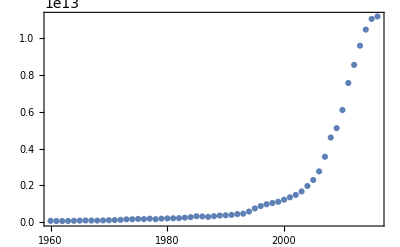

```mathematica
DateListPlot[
CountryData["China", {"GDP", All}], Joined->False]
```

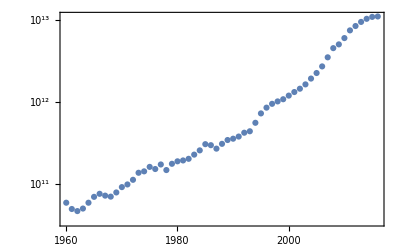

```mathematica
DateListLogPlot[
CountryData["China", {"GDP", All}], Joined->False]
```

```mathematica
Quantity[4, "Hours"]+Quantity[14, "Seconds"]
```

14414 s

```mathematica
(Quantity[4, "Hours"]+Quantity[14, "Seconds"])/2.5
```

5765.6 s

```mathematica
UnitConvert[Quantity[5765.6,"Seconds"],MixedRadix["Hours","Minutes","Seconds"]]
```

1 36

```mathematica
UnitConvert[Quantity[5765.6,"Seconds"],MixedRadix[{"Hours","Minutes","Seconds"}]]
```

$Failed

```mathematica
UnitConvert[Quantity[5765.6,"Seconds"],MixedRadix["Hours","Minutes","Seconds"]]
```

1 36

```mathematica
UnitConvert[
Quantity[
(Quantity[4, "Hours"]+Quantity[14, "Seconds"])/3,
"Seconds"],
MixedRadix["Hours","Minutes","Seconds"]]
```

$Failed

```mathematica
(Quantity[4, "Hours"]+Quantity[14, "Seconds"])/3
```

14414/3 s

```mathematica
N[Quantity[14414/3,"Seconds"]]
```

4804.67 s

```mathematica
UnitConvert[Quantity[4804.666666666667,"Seconds"],MixedRadix["Hours","Minutes","Seconds"]]
```

1 20

```mathematica
√-1
```

ⅈ

```mathematica
ⅈ^2
```

-1

```mathematica
UnitConvert[Quantity[359, "Kilometers"], "Miles"]
```

5609375/25146 mi

```mathematica
N[Quantity[5609375/25146,"Miles"]]
```

223.072 mi

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
DateListLogPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

-Graphics-

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}]]]
```

{{{1984,11,6},-0.79},{{1984,11,7},-0.25},8698,{{2019,5,6},-159.533},{{2019,5,7},-20.4366}}
 |  |  |  |

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
Differences@
Map[Last,list]
]]
```

{-0.79,-0.25,0.,-0.24,8694,127.224,-40.7067,-159.533,-20.4366}
 |  |  |  |

```mathematica
Standardize[%75]
```

{-0.044673,-0.0302626,-0.0235911,8697,-4.2809,-0.568962}
 |  |  |  |

```mathematica
Fourier[%82]
```

{1.90424×10^-16-1.52339×10^-16 ⅈ,8700,1.00395+0.485981 ⅈ}
 |  |  |  |

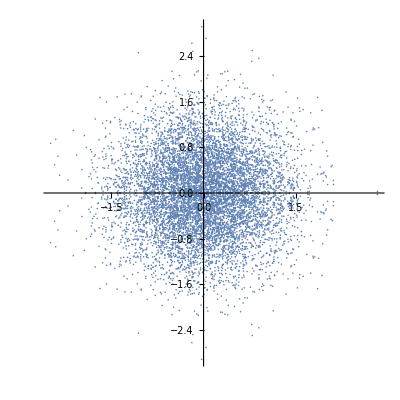

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%83,AspectRatio->1]
```

```mathematica
ContinuousWaveletTransform[%75]
```

ContinuousWaveletData[<<CWT>>, <12,4>, {8702}]

```mathematica
WaveletScalogram[%80]
```

-Graphics-

```mathematica
AndersonDarlingTest[%75]
```

0.

```mathematica
EmpiricalDistribution[%75]
```

DataDistribution[…]

```mathematica
PDF[%77,x]
```

0.000114916 Boole[-355.49==x]+7369+0.000114916 Boole[361.436==x]
 |  |  |  |

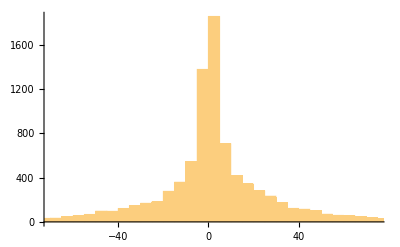

```mathematica
Histogram[%75]
```

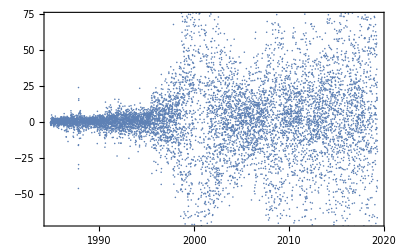

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
DateListPlot[
Transpose[{
Map[First,list][[;;-2]],
Differences@
Map[Last,list]
}], Joined->False]]]
```

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
Variance@
Differences@
Map[Last,list]
]]
```

1404.21

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
With[{diff=Differences@Map[Last,list]},
Table[func->func[diff], {func, {Min, Max,Mean,Median,Variance}}]
]]]
```

{Min→-355.49,Max→361.436,Mean→0.884024,Median→0.8828,Variance→1404.21}

```mathematica
With[{index="^IXIC"},
With[{list=FinancialData[index, "Price", All]},
With[{diff=Differences@Map[Last,list]},
Table[func->func[diff], {func, 
{Min, Max,Mean,Median,Variance, StandardDeviation}}]
]]]
```

{Min→-355.49,Max→361.436,Mean→0.884024,Median→0.8828,Variance→1404.21,StandardDeviation→37.4728}

```mathematica
FinancialData["USD", "Price"]
```

FinancialData::notdate: Price is not a valid date range for FinancialData.

1

```mathematica
MovingAverage[
Map[Last,FinancialData["^DJI", "Price", All]], 20]
```

{248.794,249.495,250.369,22737,26413.7,26404.5,26388.1}
 |  |  |  |

```mathematica
CountryData[CountryData[], "GDP"]
```

$Failed

```mathematica
Map[
CountryData[#, "GDP"]&,
CountryData[]]
```

{1.9469×10^10 $,Missing[NotAvailable],1.18639×10^10 $,1.59049×10^11 $,6.58×10^8 $,2.85852×10^9 $,1.02643×10^11 $,2.11174×10^8 $,1.46014×10^9 $,5.48055×10^11 $,1.05723×10^10 $,2.58446×10^9 $,1.20462×10^12 $,3.908×10^11 $,3.78477×10^10 $,1.12618×10^10 $,3.21791×10^10 $,2.21415×10^11 $,4.451×10^9 $,4.74072×10^10 $,4.67956×10^11 $,1.7411×10^9 $,8.58303×10^9 $,5.57371×10^9 $,2.21264×10^9 $,3.38064×10^10 $,Missing[NotAvailable],1.69103×10^10 $,1.55811×10^10 $,Missing[NotAvailable],1.79619×10^12 $,Missing[NotAvailable],9.0919×10^8 $,1.5492×10^10 $,5.32379×10^10 $,1.16932×10^10 $,3.00703×10^9 $,2.00167×10^10 $,3.22175×10^10 $,1.52976×10^12 $,1.82702×10^9 $,3.20703×10^9 $,1.75612×10^9 $,9.60076×10^9 $,2.47028×10^11 $,1.11991×10^13 $,Missing[NotAvailable],Missing[NotAvailable],2.82463×10^11 $,6.16654×10^8 $,2.4776×10^8 $,5.11067×10^10 $,5.0715×10^10 $,8.71328×10^10 $,2.871×10^9 $,2.0047×10^10 $,1.95305×10^11 $,3.19309×10^10 $,3.069×10^11 $,1.727×10^9 $,5.81484×10^8 $,7.15836×10^10 $,1.78297×10^9 $,9.8614×10^10 $,3.32791×10^11 $,2.67975×10^10 $,1.06848×10^10 $,2.60774×10^9 $,2.33379×10^10 $,7.23742×10^10 $,1.051×10^8 $,2.61346×10^9 $,4.70363×10^9 $,2.38503×10^11 $,2.46545×10^12 $,1.551×10^9 $,3.44754×10^9 $,Missing[NotAvailable],1.42136×10^10 $,9.64599×10^8 $,7.68×10^8 $,1.4378×10^10 $,3.4778×10^12 $,4.26898×10^10 $,1.106×10^9 $,1.92691×10^11 $,2.22038×10^9 $,1.05619×10^9 $,3.513×10^9 $,5.793×10^9 $,6.87633×10^10 $,2.742×10^9 $,8.20025×10^9 $,1.16494×10^9 $,3.5024×10^9 $,8.02264×10^9 $,2.15169×10^10 $,3.09929×10^11 $,1.25817×10^11 $,2.00474×10^10 $,2.26379×10^12 $,9.32259×10^11 $,4.18977×10^11 $,1.71489×10^11 $,3.04819×10^11 $,6.79242×10^9 $,2.96075×10^11 $,1.85891×10^12 $,3.63726×10^10 $,1.40569×10^10 $,4.94016×10^12 $,5.1×10^9 $,3.86547×10^10 $,1.37278×10^11 $,7.0529×10^10 $,1.81551×10^8 $,6.64989×10^9 $,1.10876×10^11 $,6.55129×10^9 $,1.59033×10^10 $,2.75727×10^10 $,4.95988×10^10 $,2.29132×10^9 $,2.101×10^9 $,2.91527×10^10 $,6.28917×10^9 $,4.27389×10^10 $,5.86313×10^10 $,4.48026×10^10 $,1.08996×10^10 $,1.00012×10^10 $,5.43304×10^9 $,2.96536×10^11 $,4.22421×10^9 $,1.4035×10^10 $,1.0999×10^10 $,1.94498×10^8 $,6.117×10^9 $,4.7393×10^9 $,1.21684×10^10 $,4.668×10^8 $,1.04692×10^12 $,3.29896×10^8 $,6.55116×10^9 $,6.07488×10^9 $,1.11835×10^10 $,4.37413×10^9 $,5.54398×10^7 $,1.03606×10^11 $,1.10149×10^10 $,6.48655×10^10 $,1.09479×10^10 $,6.34793×10^7 $,2.1132×10^10 $,7.77228×10^11 $,2.68235×10^9 $,1.84969×10^11 $,1.26926×10^10 $,7.52839×10^9 $,4.04653×10^11 $,1.001×10^7 $,Missing[NotAvailable],1.242×10^9 $,1.22782×10^10 $,3.71076×10^11 $,6.62934×10^10 $,2.78913×10^11 $,3.10248×10^8 $,5.51877×10^10 $,2.02132×10^10 $,2.74241×10^10 $,1.92207×10^11 $,3.04905×10^11 $,Missing[NotAvailable],4.71364×10^11 $,2.04837×10^11 $,1.03135×10^11 $,1.52452×10^11 $,7.83351×10^9 $,1.09×10^10 $,1.87592×10^11 $,1.28316×10^12 $,8.37605×10^9 $,Missing[NotAvailable],1.8×10^7 $,9.09855×10^8 $,1.66708×10^9 $,Missing[NotAvailable],4.83×10^7 $,7.68224×10^8 $,7.86356×10^8 $,1.59071×10^9 $,3.42782×10^8 $,6.46438×10^11 $,1.46837×10^10 $,3.82999×10^10 $,1.42732×10^9 $,3.73659×10^9 $,2.96976×10^11 $,7.934×10^8 $,8.97686×10^10 $,4.47086×10^10 $,1.20213×10^9 $,6.217×10^9 $,2.95456×10^11 $,Missing[NotAvailable],1.41125×10^12 $,9.01522×10^9 $,1.23726×10^12 $,8.13219×10^10 $,9.55844×10^10 $,3.27843×10^9 $,Missing[NotAvailable],3.72065×10^9 $,5.1446×10^11 $,6.68851×10^11 $,4.0405×10^10 $,4.27×10^11 $,6.95166×10^9 $,4.73401×10^10 $,4.07026×10^11 $,4.4×10^9 $,1.5×10^6 $,4.01562×10^8 $,2.78057×10^10 $,4.20625×10^10 $,8.63712×10^11 $,3.61799×10^10 $,1.38074×10^9 $,3.42189×10^7 $,2.40789×10^10 $,9.32705×10^10 $,3.48743×10^11 $,2.6479×10^12 $,1.86245×10^13 $,Missing[NotAvailable],3.765×10^9 $,5.24197×10^10 $,6.72203×10^10 $,7.73503×10^8 $,Missing[NotAvailable],4.82359×10^11 $,2.05276×10^11 $,6.×10^7 $,1.33971×10^10 $,Missing[NotAvailable],3.59545×10^10 $,2.1064×10^10 $,1.662×10^10 $}

```mathematica
DeleteMissing@
Map[
CountryData[#, "GDP"]&,
CountryData[]]
```

{1.9469×10^10 $,1.18639×10^10 $,1.59049×10^11 $,6.58×10^8 $,2.85852×10^9 $,1.02643×10^11 $,2.11174×10^8 $,1.46014×10^9 $,5.48055×10^11 $,1.05723×10^10 $,2.58446×10^9 $,1.20462×10^12 $,3.908×10^11 $,3.78477×10^10 $,1.12618×10^10 $,3.21791×10^10 $,2.21415×10^11 $,4.451×10^9 $,4.74072×10^10 $,4.67956×10^11 $,1.7411×10^9 $,8.58303×10^9 $,5.57371×10^9 $,2.21264×10^9 $,3.38064×10^10 $,1.69103×10^10 $,1.55811×10^10 $,1.79619×10^12 $,9.0919×10^8 $,1.5492×10^10 $,5.32379×10^10 $,1.16932×10^10 $,3.00703×10^9 $,2.00167×10^10 $,3.22175×10^10 $,1.52976×10^12 $,1.82702×10^9 $,3.20703×10^9 $,1.75612×10^9 $,9.60076×10^9 $,2.47028×10^11 $,1.11991×10^13 $,2.82463×10^11 $,6.16654×10^8 $,2.4776×10^8 $,5.11067×10^10 $,5.0715×10^10 $,8.71328×10^10 $,2.871×10^9 $,2.0047×10^10 $,1.95305×10^11 $,3.19309×10^10 $,3.069×10^11 $,1.727×10^9 $,5.81484×10^8 $,7.15836×10^10 $,1.78297×10^9 $,9.8614×10^10 $,3.32791×10^11 $,2.67975×10^10 $,1.06848×10^10 $,2.60774×10^9 $,2.33379×10^10 $,7.23742×10^10 $,1.051×10^8 $,2.61346×10^9 $,4.70363×10^9 $,2.38503×10^11 $,2.46545×10^12 $,1.551×10^9 $,3.44754×10^9 $,1.42136×10^10 $,9.64599×10^8 $,7.68×10^8 $,1.4378×10^10 $,3.4778×10^12 $,4.26898×10^10 $,1.106×10^9 $,1.92691×10^11 $,2.22038×10^9 $,1.05619×10^9 $,3.513×10^9 $,5.793×10^9 $,6.87633×10^10 $,2.742×10^9 $,8.20025×10^9 $,1.16494×10^9 $,3.5024×10^9 $,8.02264×10^9 $,2.15169×10^10 $,3.09929×10^11 $,1.25817×10^11 $,2.00474×10^10 $,2.26379×10^12 $,9.32259×10^11 $,4.18977×10^11 $,1.71489×10^11 $,3.04819×10^11 $,6.79242×10^9 $,2.96075×10^11 $,1.85891×10^12 $,3.63726×10^10 $,1.40569×10^10 $,4.94016×10^12 $,5.1×10^9 $,3.86547×10^10 $,1.37278×10^11 $,7.0529×10^10 $,1.81551×10^8 $,6.64989×10^9 $,1.10876×10^11 $,6.55129×10^9 $,1.59033×10^10 $,2.75727×10^10 $,4.95988×10^10 $,2.29132×10^9 $,2.101×10^9 $,2.91527×10^10 $,6.28917×10^9 $,4.27389×10^10 $,5.86313×10^10 $,4.48026×10^10 $,1.08996×10^10 $,1.00012×10^10 $,5.43304×10^9 $,2.96536×10^11 $,4.22421×10^9 $,1.4035×10^10 $,1.0999×10^10 $,1.94498×10^8 $,6.117×10^9 $,4.7393×10^9 $,1.21684×10^10 $,4.668×10^8 $,1.04692×10^12 $,3.29896×10^8 $,6.55116×10^9 $,6.07488×10^9 $,1.11835×10^10 $,4.37413×10^9 $,5.54398×10^7 $,1.03606×10^11 $,1.10149×10^10 $,6.48655×10^10 $,1.09479×10^10 $,6.34793×10^7 $,2.1132×10^10 $,7.77228×10^11 $,2.68235×10^9 $,1.84969×10^11 $,1.26926×10^10 $,7.52839×10^9 $,4.04653×10^11 $,1.001×10^7 $,1.242×10^9 $,1.22782×10^10 $,3.71076×10^11 $,6.62934×10^10 $,2.78913×10^11 $,3.10248×10^8 $,5.51877×10^10 $,2.02132×10^10 $,2.74241×10^10 $,1.92207×10^11 $,3.04905×10^11 $,4.71364×10^11 $,2.04837×10^11 $,1.03135×10^11 $,1.52452×10^11 $,7.83351×10^9 $,1.09×10^10 $,1.87592×10^11 $,1.28316×10^12 $,8.37605×10^9 $,1.8×10^7 $,9.09855×10^8 $,1.66708×10^9 $,4.83×10^7 $,7.68224×10^8 $,7.86356×10^8 $,1.59071×10^9 $,3.42782×10^8 $,6.46438×10^11 $,1.46837×10^10 $,3.82999×10^10 $,1.42732×10^9 $,3.73659×10^9 $,2.96976×10^11 $,7.934×10^8 $,8.97686×10^10 $,4.47086×10^10 $,1.20213×10^9 $,6.217×10^9 $,2.95456×10^11 $,1.41125×10^12 $,9.01522×10^9 $,1.23726×10^12 $,8.13219×10^10 $,9.55844×10^10 $,3.27843×10^9 $,3.72065×10^9 $,5.1446×10^11 $,6.68851×10^11 $,4.0405×10^10 $,4.27×10^11 $,6.95166×10^9 $,4.73401×10^10 $,4.07026×10^11 $,4.4×10^9 $,1.5×10^6 $,4.01562×10^8 $,2.78057×10^10 $,4.20625×10^10 $,8.63712×10^11 $,3.61799×10^10 $,1.38074×10^9 $,3.42189×10^7 $,2.40789×10^10 $,9.32705×10^10 $,3.48743×10^11 $,2.6479×10^12 $,1.86245×10^13 $,3.765×10^9 $,5.24197×10^10 $,6.72203×10^10 $,7.73503×10^8 $,4.82359×10^11 $,2.05276×10^11 $,6.×10^7 $,1.33971×10^10 $,3.59545×10^10 $,2.1064×10^10 $,1.662×10^10 $}

```mathematica
Total@
DeleteMissing@
Map[
CountryData[#, "GDP"]&,
CountryData[]]
```

7.5726×10^13 $

```mathematica
QuantityMagnitude[Quantity[7.572599898586616*^13,("USDollars")/("Years")]]
```

7.5726×10^13

```mathematica
(Total@
DeleteMissing@
Map[
CountryData[#, "GDP"]&,
CountryData[]])/(Total@
DeleteMissing@
Map[
CountryData[#, "Population"]&,
CountryData[]])
```

10026.5 $

```mathematica
Total@
DeleteMissing@
Map[
CountryData[#, "Population"]&,
CountryData[]]
```

7552596367 people

```mathematica
CountryData["UnitedStates", {"Population", 2010}]
```

308641391 people

```mathematica
Table[
CountryData["UnitedStates", {"Population", i}],
{i, 2000, 2014, 1}]
```

{281982778 people,284852391 people,287506847 people,290027624 people,292539324 people,295129501 people,297827356 people,300595175 people,303374067 people,306076362 people,308641391 people,311051373 people,313335423 people,315536676 people,317718779 people}

```mathematica
Table[
(Total@
DeleteMissing@
Map[
CountryData[#, {"GDP", i}]&,
CountryData[]])/(Total@
DeleteMissing@
Map[
CountryData[#, {"Population", i}]&,
CountryData[]]),
{i, 1960, 2018,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{382.139 $,390.229 $,418.899 $,442.285 $,475.123 $,509.807 $,541.978 $,566.593 $,600.49 $,647.749 $,750.64 $,814.766 $,920.931 $,1100.07 $,1243.96 $,1363.44 $,1456.46 $,1617.82 $,1870.64 $,2134.66 $,2393.69 $,2414.31 $,2350.89 $,2361.58 $,2407.45 $,2490.76 $,2894.83 $,3250.99 $,3574.31 $,3778.97 $,4225.94 $,4347.85 $,4540.73 $,4561.86 $,4826.76 $,5305.82 $,5348.08 $,5254.65 $,5174.09 $,5296.85 $,5396.92 $,5299.68 $,5436.13 $,6035.96 $,6719.64 $,7237.24 $,7690.84 $,8618.51 $,9272.88 $,8737.16 $,9459.11 $,10311.7 $,10432.2 $,10595. $,10719.6 $,9881.18 $,9777.72 $,0 per person,Indeterminate}

```mathematica
Table[
i->(Total@
DeleteMissing@
Map[
CountryData[#, {"GDP", i}]&,
CountryData[]])/(Total@
DeleteMissing@
Map[
CountryData[#, {"Population", i}]&,
CountryData[]]),
{i, 1960, 2018,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{1960→382.139 $,1961→390.229 $,1962→418.899 $,1963→442.285 $,1964→475.123 $,1965→509.807 $,1966→541.978 $,1967→566.593 $,1968→600.49 $,1969→647.749 $,1970→750.64 $,1971→814.766 $,1972→920.931 $,1973→1100.07 $,1974→1243.96 $,1975→1363.44 $,1976→1456.46 $,1977→1617.82 $,1978→1870.64 $,1979→2134.66 $,1980→2393.69 $,1981→2414.31 $,1982→2350.89 $,1983→2361.58 $,1984→2407.45 $,1985→2490.76 $,1986→2894.83 $,1987→3250.99 $,1988→3574.31 $,1989→3778.97 $,1990→4225.94 $,1991→4347.85 $,1992→4540.73 $,1993→4561.86 $,1994→4826.76 $,1995→5305.82 $,1996→5348.08 $,1997→5254.65 $,1998→5174.09 $,1999→5296.85 $,2000→5396.92 $,2001→5299.68 $,2002→5436.13 $,2003→6035.96 $,2004→6719.64 $,2005→7237.24 $,2006→7690.84 $,2007→8618.51 $,2008→9272.88 $,2009→8737.16 $,2010→9459.11 $,2011→10311.7 $,2012→10432.2 $,2013→10595. $,2014→10719.6 $,2015→9881.18 $,2016→9777.72 $,2017→0 per person,2018→Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Quantity::compat: 1/People and USDollars/(People Years) are incompatible units

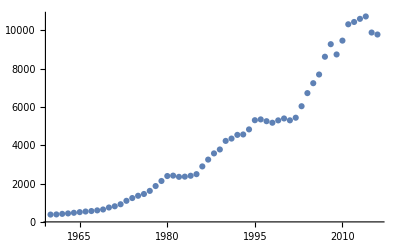

```mathematica
ListPlot@
Table[
{i,(Total@
DeleteMissing@
Map[
CountryData[#, {"GDP", i}]&,
CountryData[]])/(Total@
DeleteMissing@
Map[
CountryData[#, {"Population", i}]&,
CountryData[]])},
{i, 1960, 2018,1}]
```